# Make absorbtion matrices

```mathematica
(*Make a list of initial conditions you want*)
```

```mathematica
mat2elem[AB_,Ab_,aB_,ab_,n_]:=(ab)*n*n*n+(aB)*n*n+(Ab)*n+AB+1
```

```mathematica
elem2mat[elem_,n_]:=elem2mat[elem,n]=Block[{out},
out=Table[0,{i,1,4}];
out[[1]]=Mod[elem-1,n];
out[[2]]=Mod[Floor[(elem-1)/n],n];
out[[3]]=Mod[Floor[(elem-1)/(n*n)],n];
out[[4]]=Mod[Floor[(elem-1)/(n*n*n)],n];
out
]
```

```mathematica
initlist=Flatten[Table[{{0,i,j,0},mat2elem[0,i,j,0,10]},{i,1,9},{j,0,9}],1];
```

```mathematica
absorblist1=Flatten[Table[{{i,9,j,k},mat2elem[i,9,j,k,10]},{i,0,9},{j,0,9},{k,0,9}],2];
absorblist2=Flatten[Table[{{9,i,j,k},mat2elem[9,i,j,k,10]},{i,0,8},{j,0,9},{k,0,9}],2];
absorblist=Join[{{{0,0,0,0},1}},absorblist1,absorblist2];
```

## Get absorbtionmatrices

```mathematica
datar050=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r050.mat"][[1]];
datar050Normal=Normal[datar050[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar050];
```

```mathematica
datar040=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r040.mat"][[1]];
datar040Normal=Normal[datar040[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar040]
```

```mathematica
datar030=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r030.mat"][[1]];
datar030Normal=Normal[datar030[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar030]
```

```mathematica
datar020=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r020.mat"][[1]];
datar020Normal=Normal[datar020[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar020]
```

```mathematica
datar010=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r010.mat"][[1]];
datar010Normal=Normal[datar010[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar010]
```

```mathematica
datar005=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r005.mat"][[1]];
datar005Normal=Normal[datar005[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar005]
```

```mathematica
datar000=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r000.mat"][[1]];
datar000Normal=Normal[datar000[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar000]
```

## ProjectF for absorbstates

```mathematica
Clear[projectF]
projectF[state_,s_,r_]:=projectF[state,s,r]=Block[{out,sum,fAB,fAb,faB,fab,fABn,fAbn,faBn,fabn,Wbar},
out=Table[0,{i,1,4}];
sum = Total[state];
fAB=state[[1]]/sum;
fAb=state[[2]]/sum;
faB=state[[3]]/sum;
fab=state[[4]]/sum;
For[i=1,i≤50,++i,
Wbar=fAB*(1+s)+fAb*(1+s)+faB+fab;
fABn=(fAB fAB (1+s)(1+s)+fAB faB(1+s)+fAB fAb(1+s)(1+s)+fAB fab(1+s)(1-r)+faB fAb(1+s)r)/(Wbar Wbar);
fAbn=(fAb fAb (1+s)(1+s)+fAb fab(1+s)+fAb fAB(1+s)(1+s)+fAB fab(1+s)r+faB fAb(1+s)(1-r))/(Wbar Wbar);
faBn=(faB faB +faB fab+faB fAB(1+s)+fAB fab(1+s)r+faB fAb(1+s)(1-r))/(Wbar Wbar);
fabn=(fab fab +fab faB+fab fAb(1+s)+fAB fab(1+s)(1-r)+faB fAb(1+s)r)/(Wbar Wbar);
fAB=fABn;
fAb=fAbn;
faB=faBn;
fab=fabn;
];
out[[1]]=fAB;
out[[2]]=fAb;
out[[3]]=faB;
out[[4]]=fab;
out
]
```

```mathematica
Clear[MakeProjectionTable]
MakeProjectionTable[r_]:=MakeProjectionTable[r]=Table[projectF[absorblist[[i,1]],0.22,r],{i,1,Length[absorblist]}];
```

## Calculate expected F

```mathematica
Clear[fun];
fun[absorbvec_,r_]:=Block[{out,state,i,tableproject},
out=0;
tableproject=MakeProjectionTable[r];
For[i=2,i≤ Length[absorbvec],++i,
If[absorbvec[[i]]≠0,
out+=absorbvec[[i]]/(1-absorbvec[[1]])(tableproject[[i]][[1]])/(tableproject[[i]][[1]]+tableproject[[i]][[2]]);
]
];
out
]
```

```mathematica
rdetermindata =Table[{r,(projectF[{0,1,9,0},0.22,r][[1]])/(projectF[{0,1,9,0},0.22,r][[1]]+projectF[{0,1,9,0},0.22,r][[2]])},{r,0,0.5,0.01}];
```

```mathematica
rlistplot={{0.5,fun[datar050Normal[[;;,10]],0.5]},
{0.4,fun[datar040Normal[[;;,10]],0.4]},
{0.3,fun[datar030Normal[[;;,10]],0.3]},
{0.2,fun[datar020Normal[[;;,10]],0.2]},
{0.1,fun[datar010Normal[[;;,10]],0.1]},
{0.05,fun[datar005Normal[[;;,10]],0.05]},
{0.0,fun[datar000Normal[[;;,10]],0.0]}}
```

{{0.5,0.582509},{0.4,0.526481},{0.3,0.454951},{0.2,0.360089},{0.1,0.224996},{0.05,0.129942},{0.,0.}}

```mathematica
Table[{r,fun[{0,1,9,0},r]},{r,0,0.5,0.1}]
```

{{0.,0.},{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.}}

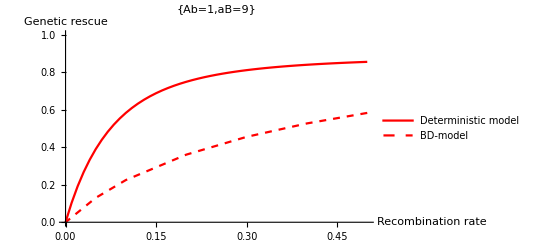

```mathematica
plot=Legended[Show[{
ListLinePlot[rlistplot,PlotRange->{Automatic,{0,1}},AxesLabel->{"Recombination rate","Genetic rescue"},PlotStyle->{Red,Dashed},PlotLabel->{"Ab=1,aB=9"}],
ListLinePlot[rdetermindata,PlotStyle->{Red}]
}
],LineLegend[{
{Red},{Red,Dashed},NULL
},
{
"Deterministic model",
"BD-model"
}
]
]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Matlab/Figures/recombinationplot.eps",plot];
```

```mathematica
resultsr050=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar050Normal[[;;,i]],0.5]},{i,1,Length[initlist]}];plotr050=ListPlot3D[resultsr050,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr040=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar040Normal[[;;,i]],0.4]},{i,1,Length[initlist]}];plotr040=ListPlot3D[resultsr040,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr030=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar030Normal[[;;,i]],0.3]},{i,1,Length[initlist]}];plotr030=ListPlot3D[resultsr030,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr020=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar020Normal[[;;,i]],0.2]},{i,1,Length[initlist]}];plotr020=ListPlot3D[resultsr020,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr010=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar010Normal[[;;,i]],0.1]},{i,1,Length[initlist]}];plotr010=ListPlot3D[resultsr010,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr005=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar005Normal[[;;,i]],0.05]},{i,1,Length[initlist]}];plotr005=ListPlot3D[resultsr005,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
resultsr000=Table[{initlist[[i]][[1]][[2]],initlist[[i]][[1]][[3]],fun[datar000Normal[[;;,i]],0.0]},{i,1,Length[initlist]}];plotr000=ListPlot3D[resultsr000,PlotTheme->"BoldColor",AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]}];
```

```mathematica
final=ListPlot3D[{resultsr050,resultsr010,resultsr000},Mesh->None,PlotTheme->{"Detailed"},PlotStyle->{{Opacity[0.5]},{Opacity[0.5]},{Opacity[0.5]}},AxesLabel->{"#Ab","#aB","F"},Ticks->{Table[i,{i,0,9}], Table[i,{i,0,9}],Table[i,{i,0,1,0.1}]},PlotLegends->{"r=0.5","r=0.1","r=0"}]
```

-Graphics3D-

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Matlab/data/FAr000.csv",resultsr000];
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Matlab/Figures/Projection3DPlot2.eps",final]
```

/home/freek/Documents/temp2/Introgression/Matlab/Figures/Projection3DPlot2.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/home/freek/Documents/temp2/Introgression/Matlab/Figures/Projection3DPlot3r.eps"]]]
```